If SchubertPolynomials.m is not in the same folder as this file, replace the file paths below by the (string) relative or complete system path to the folder containing SchubertPolynomials.m. 
Copy this cell into any notebook where you want to load this package. Use “/” instead of “\\” if you are not using Windows.

```mathematica
(*Initialization block*)
Block[{packages},
packages={
"C:\\Users\\Avery\\Dropbox\\Mathematica\\Packages",(*work*)
"D:\\Dropbox\\Mathematica\\Packages",(*home*)
"/home/avery/Dropbox/Mathematica/Packages/",
NotebookDirectory[];
};
If[!SubsetQ[$Path,packages],$Path=DeleteDuplicates[Join[$Path,packages]]];
<<SchubertPolynomials.m;
];
```

```mathematica
(*Permutations are represented by lists in one-line notation*)
w={1,5,2,3,6,4};
```

```mathematica
(*Computing Schubert polynomials*)
schub=SchubertPolynomial[w];
groth=GrothendieckPolynomial[w];
doubschub=DoubleSchubertPolynomial[w];
schub
groth
```

x[1]^3 x[2]+x[1]^2 x[2]^2+x[1] x[2]^3+x[1]^3 x[3]+x[1]^2 x[2] x[3]+x[1] x[2]^2 x[3]+x[2]^3 x[3]+x[1]^3 x[4]+x[1]^2 x[2] x[4]+x[1] x[2]^2 x[4]+x[2]^3 x[4]+x[1]^3 x[5]+x[1]^2 x[2] x[5]+x[1] x[2]^2 x[5]+x[2]^3 x[5]

x[1]^3 x[2]+x[1]^2 x[2]^2-x[1]^3 x[2]^2+x[1] x[2]^3-x[1]^2 x[2]^3+x[1]^3 x[3]+x[1]^2 x[2] x[3]-2 x[1]^3 x[2] x[3]+x[1] x[2]^2 x[3]-2 x[1]^2 x[2]^2 x[3]+x[1]^3 x[2]^2 x[3]+x[2]^3 x[3]-2 x[1] x[2]^3 x[3]+x[1]^2 x[2]^3 x[3]+x[1]^3 x[4]+x[1]^2 x[2] x[4]-2 x[1]^3 x[2] x[4]+x[1] x[2]^2 x[4]-2 x[1]^2 x[2]^2 x[4]+x[1]^3 x[2]^2 x[4]+x[2]^3 x[4]-2 x[1] x[2]^3 x[4]+x[1]^2 x[2]^3 x[4]-x[1]^3 x[3] x[4]-x[1]^2 x[2] x[3] x[4]+2 x[1]^3 x[2] x[3] x[4]-x[1] x[2]^2 x[3] x[4]+2 x[1]^2 x[2]^2 x[3] x[4]-x[1]^3 x[2]^2 x[3] x[4]-x[2]^3 x[3] x[4]+2 x[1] x[2]^3 x[3] x[4]-x[1]^2 x[2]^3 x[3] x[4]+x[1]^3 x[5]+x[1]^2 x[2] x[5]-2 x[1]^3 x[2] x[5]+x[1] x[2]^2 x[5]-2 x[1]^2 x[2]^2 x[5]+x[1]^3 x[2]^2 x[5]+x[2]^3 x[5]-2 x[1] x[2]^3 x[5]+x[1]^2 x[2]^3 x[5]-x[1]^3 x[3] x[5]-x[1]^2 x[2] x[3] x[5]+2 x[1]^3 x[2] x[3] x[5]-x[1] x[2]^2 x[3] x[5]+2 x[1]^2 x[2]^2 x[3] x[5]-x[1]^3 x[2]^2 x[3] x[5]-x[2]^3 x[3] x[5]+2 x[1] x[2]^3 x[3] x[5]-x[1]^2 x[2]^3 x[3] x[5]-x[1]^3 x[4] x[5]-x[1]^2 x[2] x[4] x[5]+2 x[1]^3 x[2] x[4] x[5]-x[1] x[2]^2 x[4] x[5]+2 x[1]^2 x[2]^2 x[4] x[5]-x[1]^3 x[2]^2 x[4] x[5]-x[2]^3 x[4] x[5]+2 x[1] x[2]^3 x[4] x[5]-x[1]^2 x[2]^3 x[4] x[5]+x[1]^3 x[3] x[4] x[5]+x[1]^2 x[2] x[3] x[4] x[5]-2 x[1]^3 x[2] x[3] x[4] x[5]+x[1] x[2]^2 x[3] x[4] x[5]-2 x[1]^2 x[2]^2 x[3] x[4] x[5]+x[1]^3 x[2]^2 x[3] x[4] x[5]+x[2]^3 x[3] x[4] x[5]-2 x[1] x[2]^3 x[3] x[4] x[5]+x[1]^2 x[2]^3 x[3] x[4] x[5]

```mathematica
(*Exponents and coefficients*)
exps=Exponents[schub]
coeffs=Coefficients[schub]
```

{{3,1,0,0,0},{3,0,1,0,0},{3,0,0,1,0},{3,0,0,0,1},{2,2,0,0,0},{2,1,1,0,0},{2,1,0,1,0},{2,1,0,0,1},{1,3,0,0,0},{1,2,1,0,0},{1,2,0,1,0},{1,2,0,0,1},{0,3,1,0,0},{0,3,0,1,0},{0,3,0,0,1}}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*Code*)
LehmerCode[w]
LehmerCodeToPermutation[{0,3,0,0,1}]==w
```

{0,3,0,0,1,0}

True

{{2,2},{2,3},{2,4},{5,4}}

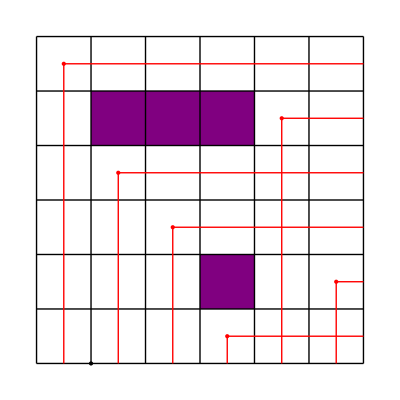

```mathematica
(*Rothe Diagarms*)
RotheDiagram[w]
DrawRotheDiagram[w]
```

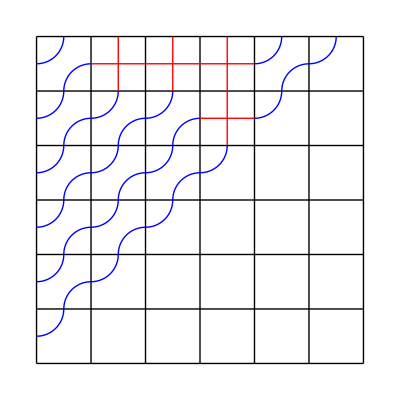
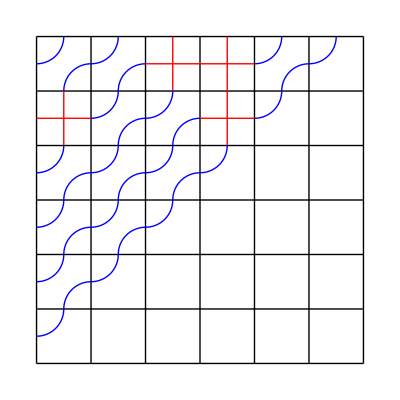
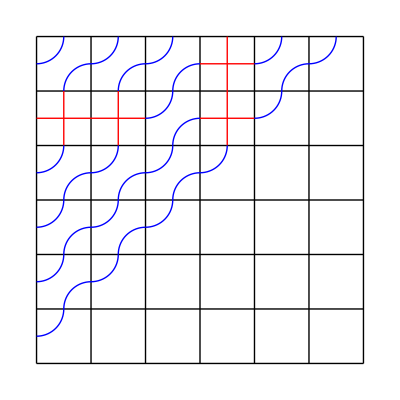
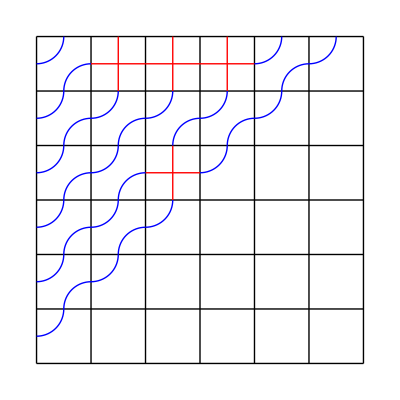
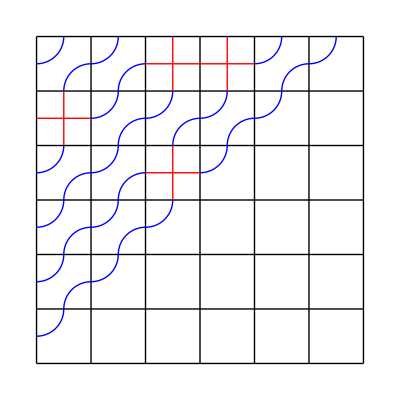
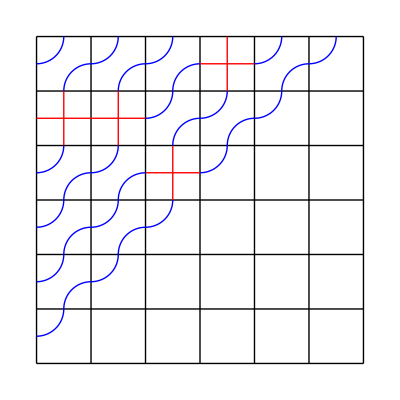
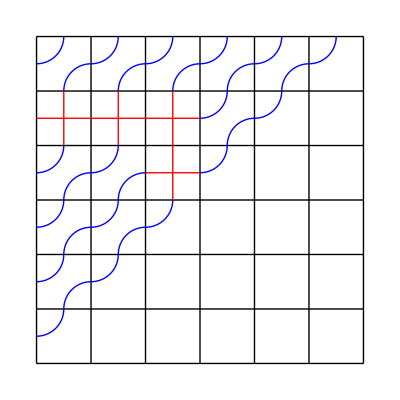
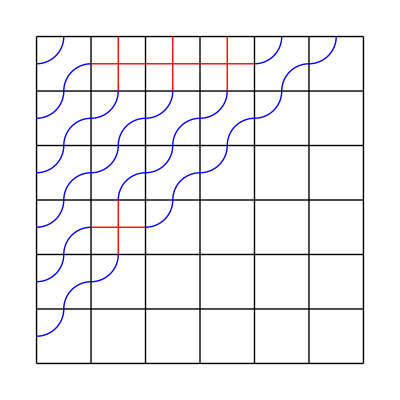

```mathematica
(*Pipe dreams*)
rpd=ReducedPipeDreams[w];
DrawPipeDream[#,CrossColor->Red,ElbowColor->Blue,Labels->False]&/@rpd
```

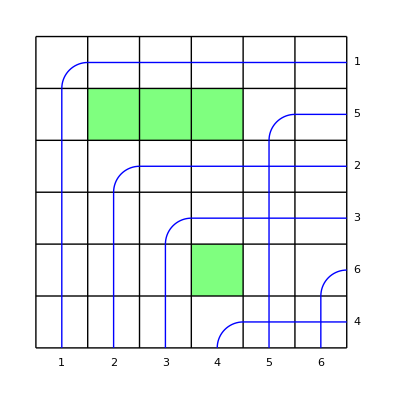
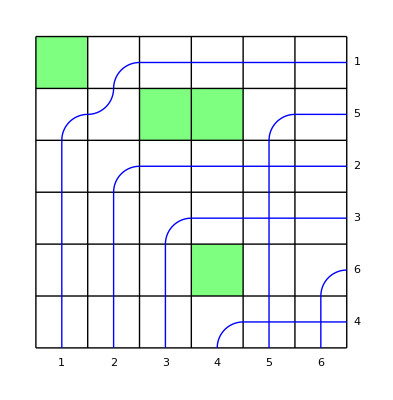
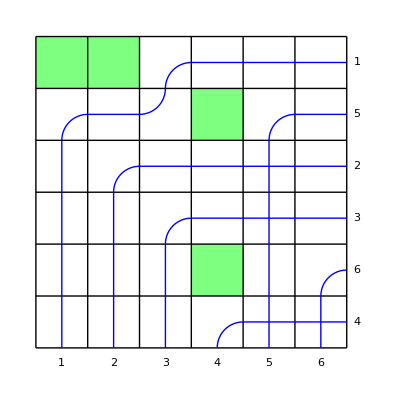
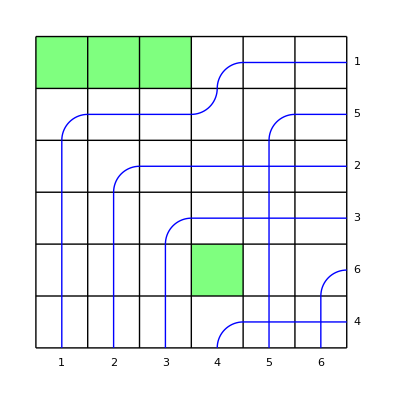
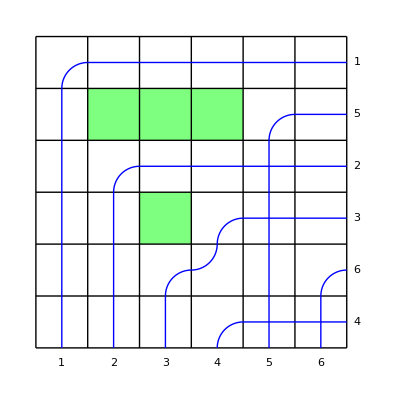
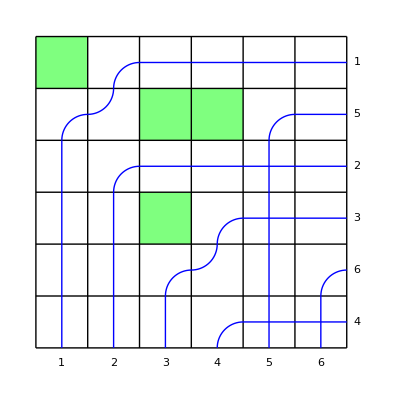
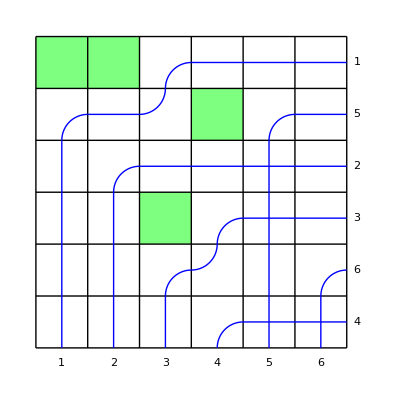
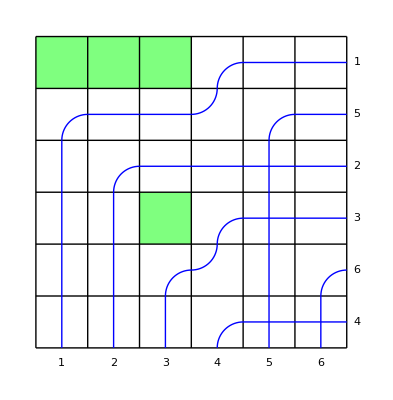

```mathematica
(*Bumpless pipe dreams; can be slow*)

bpd=BumplessPipeDreams[w];
DrawBumplessPipeDream/@bpd
```

{{0,0,0,0,0,0},{0,1,1,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

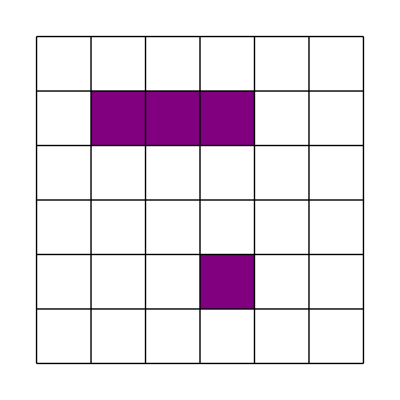
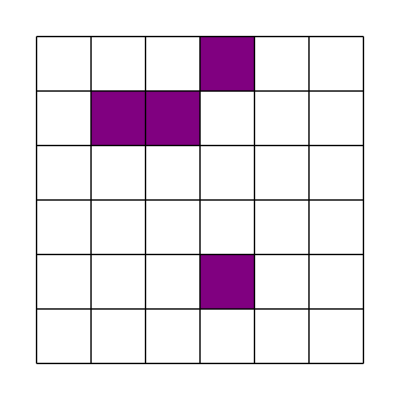
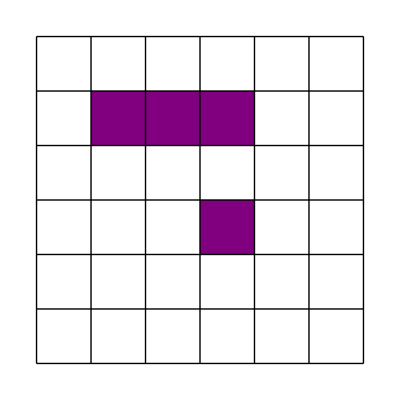
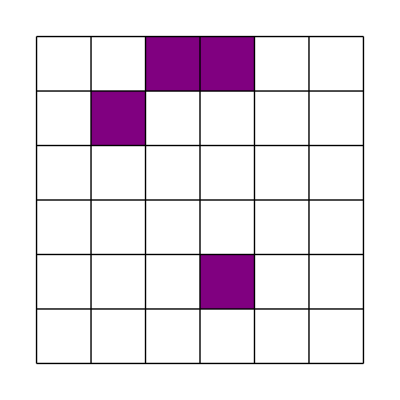
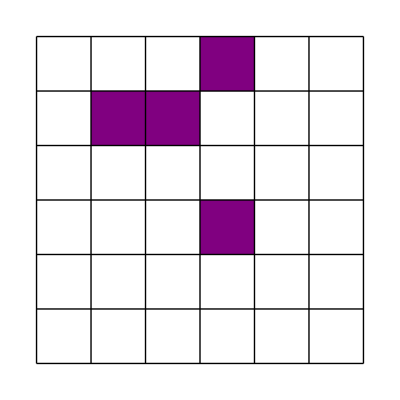
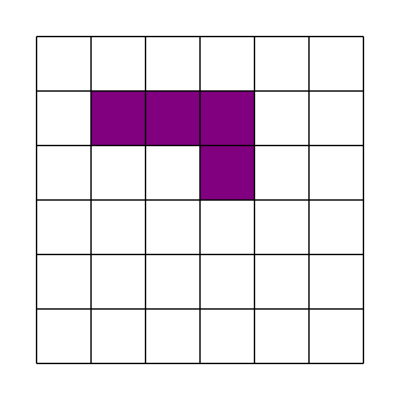
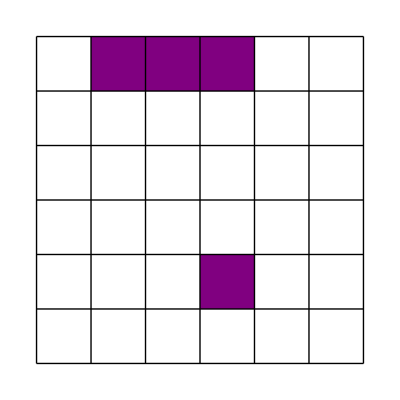
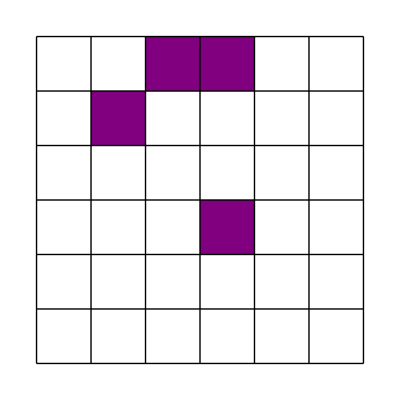

```mathematica
(*Kohnert Diagrams*)
diagrammatrix=ToZeroOneMatrix[RotheDiagram[w],{Length[w]}]
diagrammatrix//MatrixForm
kohnert=KohnertDiagrams[diagrammatrix];
DrawKohnertDiagram/@kohnert
```

```mathematica
(*Checking the Lorentzian property*)
LorentzianPolynomialQ[NormalizePolynomial[schub]]
```

True